```mathematica
Guy F. Mongelli                                                         ECHE 642;
Prof. R.M. Sankaran                                                   1/14/2013;
```

```mathematica
Problem Set #1;
```

```mathematica
Exercise 1;
```

```mathematica
Assumptions;
-Ideal behavior ;
   -Isothermal(1L in reactants is 1L in products);
```

```mathematica
ChemicalData["Propane","MoleculePlot"]
```

-Graphics3D-

```mathematica
ChemicalData["Hydrogen","MoleculePlot"]
```

-Graphics3D-

```mathematica
Based upon the following equilibrium constants being less than one, the equilibrium lies to the left.  This reaction is endothermic, since increasing the temperature, increases the equilibrium constant (Le Chatlier's Principle).;
```

```mathematica
Subscript[K, a][400]=.000521;
```

```mathematica
Subscript[K, a][500]=.0104;
```

```mathematica
Subscript[K, a][600]=.104;
```

```mathematica
Assume that the reaction is first order.;
```

```mathematica
Let species A be propane , species B be propylene, and species C be Subscript[H, 2];
```

```mathematica
Subscript[K, A]=Subscript[k, 1]/Subscript[k, 2]=(([Subscript[C, B]]_eq[Subscript[C, C]])_eq)/([Subscript[C, A]]_eq)
```

```mathematica
Then, we crate an ICE table (Initial, Change, Equilibrium) of absolute moles. One mole of reactant is assumed. The change row is determined by the stoichiometry of the reaction. As is the power that the concentration takes in the equilibrium expression
```

```mathematica
({{0, Subscript[X, A], Subscript[X, B], Subscript[X, C]}, {I, 1, 0, 0}, {C, -x, +x, +x}, {E, 1-x, x, x}});
```

```mathematica
A=({{1, 0, 0}, {-x, +x, +x}, {1-x, x, x}})
```

{{1,0,0},{-x,x,x},{1-x,x,x}}

```mathematica
The number of moles can be automatically generated through the use of the following command.
```

```mathematica
Tr[A[[3,All]]]
```

1+x

```mathematica
Then the number of moles as a function of extent of reaction in this system is given by summing the terms in the change row:
```

```mathematica
n[x_]=Simplify[1-x+x+x]
```

1+x

```mathematica
The concentrations are given as absolute moles over the number of moles total (constant-pressure assumption). This is the partial pressure.
```

```mathematica
Subscript[c, A,eq][x_]=(1-x)/n[x];
```

```mathematica
Subscript[c, B,eq][x_]=x/n[x];
```

```mathematica
Subscript[c, C,eq][x_]=x/n[x];
```

```mathematica
(Subscript[c, C,eq][x]Subscript[c, B,eq][x])/(Subscript[c, A,eq][x])
```

x^2/((1-x) (1+x))

```mathematica
Observe the solution for an arbitrary equilibrium constant.
```

```mathematica
Solve[Γ== (Subscript[c, C,eq][x]Subscript[c, B,eq][x])/(Subscript[c, A,eq][x]),x]
```

{{x→-(√Γ)/(√(1+Γ))},{x→(√Γ)/(√(1+Γ))}}

```mathematica
Ignore the negative extent of reaction.  The next line of code, looks at how the extent of reaction changes as a function of the equilibrium constant.
```

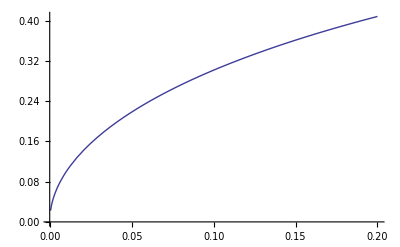

```mathematica
Plot[(√Γ)/(√(1+Γ)),{Γ,.0005,.2}]
```

```mathematica
The fraction of propane converted to propylene is x divided by the initial number of moles of propane.Since that was assumed to be one, this fraction is simply x.
```

```mathematica
x[Γ_]=(√Γ)/(√(1+Γ));
```

```mathematica
For 400^°C:
```

```mathematica
x[.000521]
```

0.0228195

```mathematica
For 500^°C:
```

```mathematica
x[.0104]
```

0.101454

```mathematica
For 600^°C:
```

```mathematica
x[.104]
```

0.306925

```mathematica
Problem 2:
```

```mathematica
Assumptions:
-Ideal behavior
-Isothermal system (heat of reaction does not cause expansion/contraction, and therefore concentration changes)
```

Assumptions:-behavior Ideal

```mathematica
ChemicalData["Oxygen","MoleculePlot"]
```

-Graphics3D-

```mathematica
ChemicalData["Water","MoleculePlot"]
```

-Graphics3D-

```mathematica
These equilibrium constants lie far to the right and indicate near completion.  Since increasing the temperature shifts equilibrium to the left, we expect that this reaction is exothermic.
```

```mathematica
Subscript[K, a][400]=1.16*10^26;
```

```mathematica
Subscript[K, a][500]=5.34*10^23;
```

```mathematica
Subscript[K, a][600]=8.31*10^21;
```

```mathematica
Clear[x]
```

```mathematica
Subscript[K, A]=Subscript[k, 1]/Subscript[k, 2]=(([Subscript[C, B]]_eq[Subscript[C, C]])_eq)/([Subscript[C, A]]_eq)
```

```mathematica
Then, we crate an ICE table (Initial, Change, Equilibrium) of absolute moles. One mole of reactant is assumed. The change row is determined by the stoichiometry of the reaction. As is the power that the concentration takes in the equilibrium expression .  Assumption: Equimolar initial concentrations of the reactants and no products present.
```

```mathematica
{{□, Subscript[X, A], Subscript[X, B], Subscript[X, C], Subscript[X, D]}, {I, 1, 1, 0, 0}, {C, -x, -x/2, +x, +x}, {E, 1-x, 1-x, x, x}}
```

```mathematica
Then the number of moles as a function of extent of reaction in this system is given by summing the terms in the change row:
```

```mathematica
n[x_]=Simplify[2-x-x+x+x]
```

2

```mathematica
The concentrations are given as absolute moles over the number of moles total (constant-pressure assumption). This is the partial pressure.
```

```mathematica
Subscript[c, A,eq][x_]=(1-x)/n[x];
```

```mathematica
Subscript[c, B,eq][x_]=(1-(x/2))/n[x];
```

```mathematica
Subscript[c, C,eq][x_]=x/n[x];
```

```mathematica
Subscript[c, D,eq][x_]=x/n[x];
```

```mathematica
(Subscript[c, C,eq][x]Subscript[c, D,eq][x])/(Subscript[c, A,eq][x](Subscript[c, B,eq][x])^(1/2))
```

x^2/(√2 (1-x) √(1-x/2))

```mathematica
Element[{x,Γ},Reals];
```

```mathematica
For 400^°C:
```

```mathematica
Solve[1.16*10^26== (Subscript[c, C,eq][x]Subscript[c, D,eq][x])/(Subscript[c, A,eq][x](Subscript[c, B,eq][x])^(1/2)),x]
```

{{x→-1.3456×10^52},{x→1.}}

```mathematica
This indicates that the reaction goes to completion.
```

```mathematica
For 500^°C:
```

```mathematica
Solve[5.34*10^23== (Subscript[c, C,eq][x]Subscript[c, D,eq][x])/(Subscript[c, A,eq][x](Subscript[c, B,eq][x])^(1/2)),x]
```

{{x→-2.85156×10^47},{x→1.}}

```mathematica
This indicates that the reaction goes to completion.
```

```mathematica
For 600^°C:
```

```mathematica
Solve[8.31*10^21== (Subscript[c, C,eq][x]Subscript[c, D,eq][x])/(Subscript[c, A,eq][x](Subscript[c, B,eq][x])^(1/2)),x]
```

{{x→-6.90561×10^43},{x→1.}}

```mathematica
This indicates that the reaction goes to completion.
```

```mathematica
Discount the negative extents of reaction.
```

```mathematica
The fraction of propane that is converted to propylene is 1 for all cases with each of these equilibrium constants.
```

```mathematica
The flame temperature of pure Propane is (2,820)^°C.  F or propane-air, 2200°C=3992°F.  Since the reaction forms water, it is likely that it is exothermic, although the heat of formation was not calculated.  If the reaction lies strongly to the right, and is exothermic, it may pose a risk of reaching combustion temperatures- at least locally and when performed at plant scale. A cooling method must be incorporated to prevent this.  Perhaps, allowing the reactor to increase in volume as the reaction progresses, if performed in a batch system- as we have comnsidered in thus far in this course.
```

```mathematica
Problem #3:
```

```mathematica
First, load each temperature set into a single data set:
```

```mathematica
The following data set, data1, will be for 323K.
```

```mathematica
data1={{0,.097},{20,.079},{40,0.069},{45,0.068}}
```

{{0,0.097},{20,0.079},{40,0.069},{45,0.068}}

```mathematica
lm1=LinearModelFit[data1,x,x]
```

FittedModel[0.0951379-0.00064335 x]

```mathematica
%45["BestFit"]
```

8.31×10^21[BestFit]

```mathematica
lm1["FitResiduals"]
```

{0.00186207,-0.00327094,-0.000403941,0.00181281}

```mathematica
The following data set, data2, will be for 298K.
```

```mathematica
data2={{0,.098},{74,.081},{98,0.078},{125,0.074},{170,0.066}}
```

{{0,0.098},{74,0.081},{98,0.078},{125,0.074},{170,0.066}}

```mathematica
lm2=LinearModelFit[data2,x,x]
```

FittedModel[0.0967618-0.000185886 x]

```mathematica
%39["BestFit"]
```

0.27466[BestFit]

```mathematica
lm2["FitResiduals"]
```

{0.00123823,-0.00200619,-0.000544923,0.000474004,0.000838884}

```mathematica
The following data set, data3, will be for 278K.
```

```mathematica
data3={{0,.093},{75,.091},{110,0.090},{176,0.088},{230,0.087}}
```

{{0,0.093},{75,0.091},{110,0.09},{176,0.088},{230,0.087}}

```mathematica
lm3=LinearModelFit[data3,x,x]
```

FittedModel[0.0929605-0.0000267382 x]

```mathematica
lm3["BestFit"]
```

0.0929605-0.0000267382 x

```mathematica
lm3["FitResiduals"]
```

{0.0000395403,0.0000449081,-0.0000192535,-0.00025453,0.000189335}

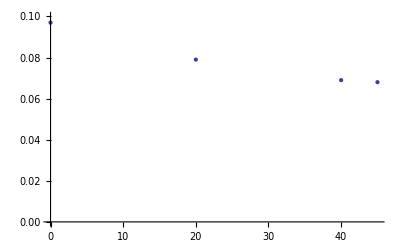

```mathematica
ListPlot[{data1,},PlotRange->{0,.1}]
```

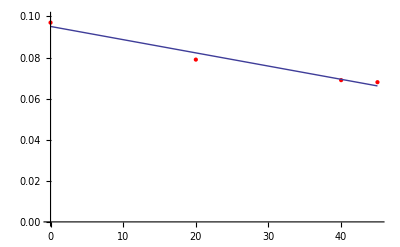

```mathematica
Show[ListPlot[lm1["Data"],PlotStyle->Red,PlotRange->{0,.1}],Plot[lm1[x],{x,0,45}]]
```

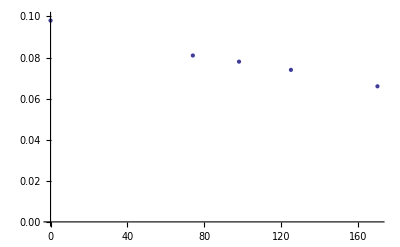

```mathematica
ListPlot[data2,PlotRange->{0,.1}]
```

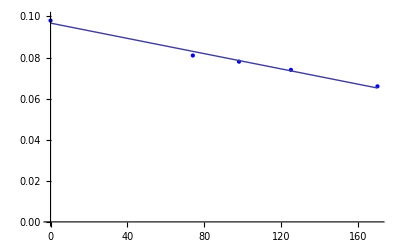

```mathematica
Show[ListPlot[lm2["Data"],PlotStyle->Blue,PlotRange->{0,.1}],Plot[lm2[x],{x,0,170}]]
```

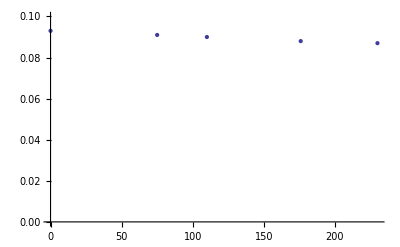

```mathematica
ListPlot[data3,PlotRange->{0,.1}]
```

```mathematica
Show[ListPlot[lm2["Data"],PlotStyle->Green,PlotRange->{0,.1}],Plot[lm2[x],{x,0,170}]]
```

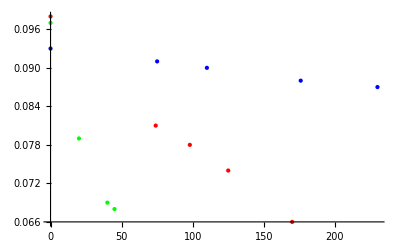

```mathematica
ListPlot[{data1,data2,data3},PlotStyle->{Green,Red,Blue}]
```

```mathematica
Discussion of the data;
```

```mathematica
At the higher temperatures, the concentration of DMB decreases to a lower level given a certain time.  In other words, the reaction rates are higher, at higher temperatures.  As a chemical engineer, this could be viewed as an advantage if operating costs are not increased too much for increased temperature, since higher conversion rates could be acheived sooner for an increase in temperature.  However, a more thorough cost-benefits analysis is required to determine exact profitability potential.  Le Chatlier's principle would then tell us that this is an endothermic reaction, since more available energy shifts the reaction towards the products.  Also, since equimolar amounts of the two reactants, DMB and acrolein were initially present, and the stoichimetric coefficiencts (υn) of these reactants are the same, the concentration of acrolein must be identical to the concentation of DMB  as the reaction progresses.  Furthermore, from this multi-temperature data set, an activation energy could be extrapolated if necessary.  This would allow us to model the reaction at other temperatures within this range and assist in the cost-benefits analysis.
```

```mathematica
The rate constant cen be solved for from the rate equation:
```

```mathematica
-Subscript[dc, A]/dt=k*Subscript[c, A]*Subscript[c, B]
```

```mathematica
Again, Subscript[c, A]=Subscript[c, B] for this reaction for all t. Therefore:
```

```mathematica
-Subscript[dc, A]/dt=k*Subscript[c, A]^2
```

```mathematica
The rate is the time derivative of the approximations above.
```

```mathematica
D[lm1["BestFit"],x]
```

-0.00064335

```mathematica
D[lm2["BestFit"],x]
```

-0.000185886

```mathematica
D[lm3["BestFit"],x]
```

-0.0000267382

```mathematica
Then create an instantaneous rate constant for each time-concentration relationship.  In the plots of this assignment, x maps onto time.
```

```mathematica
c1[x_]=D[lm1["BestFit"],x]/(lm1["BestFit"])^2
```

-0.00064335/(0.0951379-0.00064335 x)^2

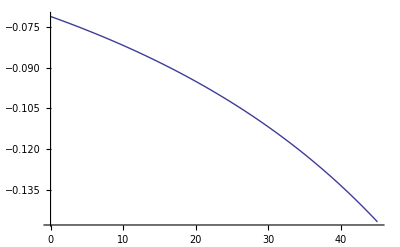

```mathematica
Plot[c1[x],{x,0,45}]
```

```mathematica
c2[x_]=D[lm2["BestFit"],x]/(lm2["BestFit"])^2
```

-0.000185886/(0.0967618-0.000185886 x)^2

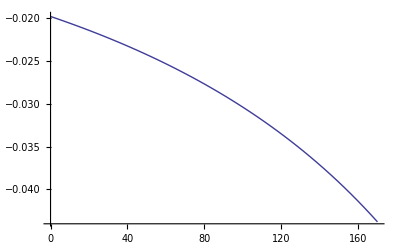

```mathematica
Plot[c2[x],{x,0,170}]
```

```mathematica
c3[x_]=D[lm3["BestFit"],x]/(lm3["BestFit"])^2
```

-0.0000267382/(0.0929605-0.0000267382 x)^2

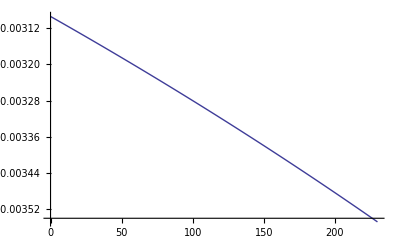

```mathematica
Plot[c3[x],{x,0,230}]
```

```mathematica
This data set indicates that the rate constant is changing over the timeframe of the reaction.  After further consideration, it is the rate constant and the fact that it is derived from raw data that must be accepted as fact.  The assumption that relaxes, then is the constant-temperature assumption.  Since the reaction is endothermic, the system will cool slightly (unless heating is provided) and the reaction rate will decrease.  Calculating the activation energy, and the enthalpy of reaction, should allow us to account for these affects, however minute they are.
```

```mathematica
Problem 4:
```

```mathematica
The rate equation is given as
```

```mathematica
Subscript[dc, A]/dt=-k*Subscript[c, A]*Subscript[c, B]^2
```

```mathematica
As seen in lecture, it is possible to eliminate Subscript[c, B] through knowledge of the stoichiometry of the reaction and the relative initial concentrations.
```

```mathematica
It is given:
```

```mathematica
Subscript[c, A,0]=.01 (* mol/L *);
```

```mathematica
Subscript[c, B,0]=3*.01 (* mol/L *)
```

0.03

```mathematica
The relationship between Subscript[c, B] and Subscript[c, A] at any given time is:
```

```mathematica
Subscript[c, B]=Subscript[c, B,0]-(Subscript[c, A,0]-Subscript[c, A])2;
```

```mathematica
Substitution into the rate equation gives
```

```mathematica
Subscript[dc, A]/dt=-k*Subscript[c, A]*(Subscript[c, B,0]-(Subscript[c, A,0]-Subscript[c, A])2)^2
```

```mathematica
This is solveable be separation of variables routes and applying the initial boundary condition.
```

```mathematica
DSolve[{Subscript[c, A]'[t]==-k*Subscript[c, A][t]*(Subscript[c, B,0]-(Subscript[c, A,0]-Subscript[c, A][t])2)^2,Subscript[c, A][0]==Subscript[c, A,0]},Subscript[c, A][t],t]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

```mathematica
∫1/(Subscript[c, A]*(Subscript[c, B,0]-(Subscript[c, A,0]-Subscript[c, A])2)^2)ⅆ Subscript[c, A]
```

0.25 (0.+40000. Log[-c_A]-40000. Log[0.005+c_A]+200./(0.005+c_A))

```mathematica
∫-kⅆt
```

-k t

```mathematica
Solve[∫1/(Subscript[c, A]*(Subscript[c, B,0]-(Subscript[c, A,0]-Subscript[c, A])2)^2)ⅆ Subscript[c, A]== ∫-kⅆt,k]
```

{{k→-(0.25 (0.+40000. Log[-1. c_A]-40000. Log[0.005+c_A]+200./(0.005+c_A)))/t}}

```mathematica
There are still degrees of freedom to be fixed.  The time and the concentration of A will hone in on the exact rate constant.
```

```mathematica
At t=10 min, Subscript[c, A]=Subscript[c, A,0]/2
```

```mathematica
Clear[k]
```

```mathematica
k=-(Log[2 *cA]-Log[cA-Subscript[c, A,0]+Subscript[c, B,0]/2]+(-2 Subscript[c, A,0]+Subscript[c, B,0])/(2 cA-2 Subscript[c, A,0]+Subscript[c, B,0]))/(t (-2 Subscript[c, A,0]+Subscript[c, B,0])^2);
```

```mathematica
t=10 (* minutes *);
```

```mathematica
cA=Subscript[c, A,0]/2(* mol/L *);
```

```mathematica
k (* mol/L/min *)
```

-500.

```mathematica
k/60 (* mol/L/sec *)
```

-8.33333